```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\fluc_T\fluctuations_T\highorder_2p1\input_h\Tpc\v1_Tc210alphap50\data

```mathematica
mf=Transpose[Import["../TemB1/BUFFER/MF.DAT"]][[1]];
T=Flatten[Table[i,{i,1,300}]];
mfdata=Transpose[{T,mf}];
```

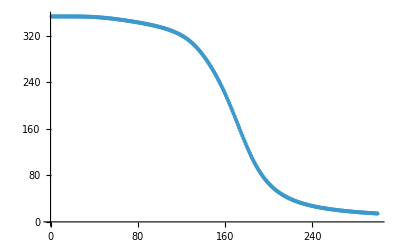

```mathematica
ListPlot[mfdata]
```

```mathematica
mfint=Interpolation[mfdata];
dmfdt=D[-mfint[x],x];
```

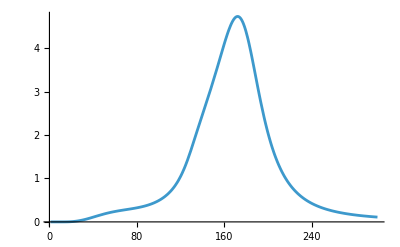

```mathematica
Plot[dmfdt,{x,1,300}]
```